```mathematica
Clear["Global`*"]
```

### 関数過去

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる:ランク) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex[PartLoop]}];
EdgeRules[Gout][[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力(動作に疑問あり) *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
NewDirectedGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築 *)
EdgeProcess={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
For[j=1,
Length[PartLoopVertexProcess]≠ Length[Pin],
j++,
If[!SubsetQ[PartLoopVertexProcess,VertexList[{EdgeRules[Gout][[SortList[[j]]]]}]],
EdgeProcess=Append[EdgeProcess,EdgeRules[Gout][[SortList[[j]]]]]
];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]]];
];
PartLoopProcess
)
```

```mathematica
DelEdgeNumOfRestPartLoop[EdgeListNum_,PartLoop_]:=DelEleList[EdgeListNum,DelEleList[EdgeNumListVertex[Subsets[VertexList[PartLoop],{2}]],EdgeNumList[PartLoop]]](* PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を枝リストの枝番号から削除する *)
```

```mathematica
NewDirectedGreedyFromSort2[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築2(枝を追加してから余分な枝を削除するアルゴリズム) *)
EdgeProcessNum={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
DelEdgeProcess={};
For[j=1,Length[PartLoopVertexProcess]< Length[Pin],j++,
EdgeProcessNum=Append[EdgeProcessNum,SortList[[j]]];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]];
DelEdge={};
For[k=1,k≤Length[PartLoopProcess],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,EdgeRules[PartLoopProcess[[k]]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
DelEdgeProcess=Append[DelEdgeProcess,DelEdge];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]]
];
PartLoopProcess
)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
PluralPartLoopByGreedyFromRank[Rank_]:=(
PartLoopProcess={};
For[i=3,Length[PartLoopProcess]==0,i++,
PartLoopProcess=FindCycle[
Graph[EdgeList[Gout][[Rank[[Range[i]]]]]],
Infinity,All]
];
EdgeRulesList[PartLoopProcess]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築 *)
```

```mathematica
DelEdgePluralPartLoop[PartLoopList_]:=(
EdgeProcessNum=EdgeNumList[Flatten[PartLoopList]];
DelEdge={};
For[k=1,k≤Length[PartLoopList],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,PartLoopList[[k]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
EdgeRulesList[FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]
)
(* Delete Edge from Plural PartLoop, 複数の部分巡回路から、PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を削除し、再度、複数の部分巡回路を見つける *)
```

```mathematica
PluralPartLoopByGreedyFromRank2[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築2(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
MostOutEdge[PartLoop_,Rank_]:=(
OutEdgeList=DelEleList[Rank,DelEleList[Rank,EdgeNumListVertex[Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]];(* OutEdgeList is Variable *)
OutEdgeList[[1]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝で最もランクが高い枝を出力(動作に疑問あり) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeNumListLine[LineList_]:=EdgeNumListVertex[ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]](* Edge Num List from Line 「Line」のリストから枝番号のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRules[Gout][[EdgeNumListLine[MeshCells[mesh,1]]]](* Edge Rules from Mesh 「MeshRegion」のリストから枝の規則を出力 *)
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin={{5.164182052947936,5.6556978234815105},{9.352434751098592,3.0419443782390143},{3.840852496934513,6.831113771983031},{1.02856252932032,6.070086670545745},{0.6900387306437814,5.4501662280876655},{6.944164458670514,0.4881941795851077},{3.6078173305349477,9.868885528489514},{7.575972630493634,6.8963310175636465},{6.1253828322156565,8.8296545837791},{6.764603406515636,5.960944653326191},{3.260832833278327,8.713094820584388},{9.285414609877435,3.6768054626103037},{2.5000307651658087,2.5397236338301212},{0.6589849700785742,3.409817357880664},{1.8056738400175547,7.839620987369251},{6.782112543993733,9.398859383537275},{7.621017148556575,2.4590831891121674},{1.4850428436791603,6.3530617858390634},{7.547225829255829,1.3600848944641264},{5.634970016409994,3.093244737740715}}(*Point input*)
```

{{5.16418,5.6557},{9.35243,3.04194},{3.84085,6.83111},{1.02856,6.07009},{0.690039,5.45017},{6.94416,0.488194},{3.60782,9.86889},{7.57597,6.89633},{6.12538,8.82965},{6.7646,5.96094},{3.26083,8.71309},{9.28541,3.67681},{2.50003,2.53972},{0.658985,3.40982},{1.80567,7.83962},{6.78211,9.39886},{7.62102,2.45908},{1.48504,6.35306},{7.54723,1.36008},{5.63497,3.09324}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

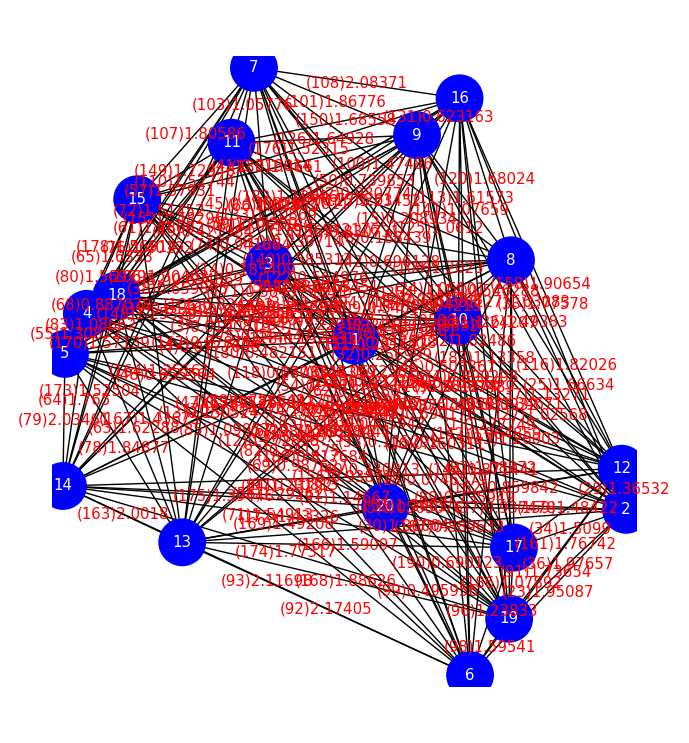

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

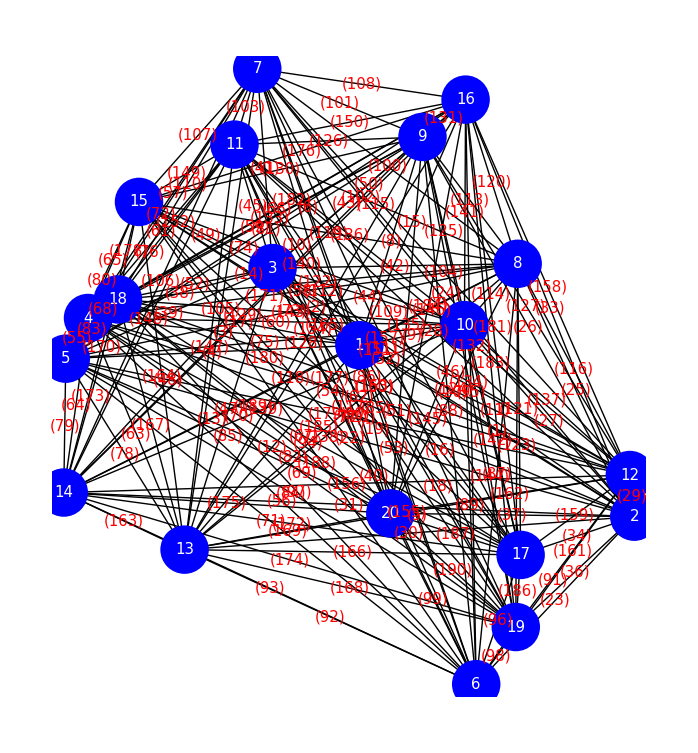

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 1→11
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

1→12 | 1→13 | 1→14 | 1→15 | 1→16 | 1→17 | 1→18 | 1→19 | 1→20 | 2→3
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 2→11 | 2→12 | 2→13
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

2→14 | 2→15 | 2→16 | 2→17 | 2→18 | 2→19 | 2→20 | 3→4 | 3→5 | 3→6
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

3→7 | 3→8 | 3→9 | 3→10 | 3→11
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{17.7747,10.0059,217.816,57.5914,108.211,16.573,149.788,17.5988,26.3142,15.0239,12.0014,23.7113,33.4429,21.607,19.5174,25.1491,49.6188,65.7981,64.1802,18.5135,25.4199,15.3838,1.79929,8.48929,2.54694,4.43595,3.80329,11.2639,0.467575,5.05189,7.58829,34.7965,3.86134,1.20994,43.0106,1.24826,3.96576,4.41501,5.62465,21.3456,9.58038,5.36638,3.91524,5.97838,10.9513,12.5004,7.75796,7.12701,5.38256,5.27726,115.894,3.45939,57.3179,17.1915,0.539708,6.29218,2.90739,13.6374,5.40365,28.7967,2.32681,52.1456,2.35676,1.52171,1.18328,6.05039,10.511,0.605442,8.14296,5.99687,5.1535,3.49625,22.2174,6.79521,137.152,2.96307,22.2793,1.85386,1.00293,1.67989,7.5217,8.01981,1.10712,6.48123,4.98187,148.036,5.9145,12.4179,7.44032,50.4617,2.278,2.25146,3.27402,12.8364,9.82066,1.68281,7.23057,0.664488,5.87859,3.36171,1.45823,5.12215,1.14085,6.98742,8.99092,5.44243,1.50287,1.54,15.6015,2.68879,26.958,155.968,1.49593,2.26667,3.79257,2.00258,16.1849,96.4217,6.20573,1.56253,3.29504,10.8237,4.3938,5.30164,2.76957,1.73829,3.70647,37.7372,12.641,3.02279,1.39462,6.38503,4.74424,8.45514,12.2343,5.36325,3.00319,11.0924,24.7883,9.05989,3.19338,3.73636,18.6472,5.35544,4.46578,8.78133,7.07825,4.7133,0.981339,2.12831,26.1435,1.99163,92.281,49.6356,5.89898,9.19387,20.0127,3.27593,1.38948,379.522,1.63871,4.29939,1.01723,4.27066,72.2765,3.21918,2.74655,2.74788,2.13356,2.91195,14.6568,4.90258,2.00452,4.05305,3.57562,3.42383,48.43,0.969159,21.4037,12.6485,5.62794,5.42629,7.12351,10.5007,12.8976,1.02091,2.34348,9.60476,6.69223,3.73964}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{29,55,68,98,178,149,79,163,186,83,103,65,34,36,159,131,101,113,107,64,108,120,161,80,96,126,23,78,152,116,173,150,169,92,114,91,61,187,63,25,110,167,168,125,57,170,76,137,130,141,166,93,158,121,100,176,52,72,175,127,142,190,115,27,33,43,37,174,164,162,123,38,26,145,148,133,172,85,30,102,71,50,124,144,136,42,49,59,182,106,39,181,99,155,87,44,70,66,119,56,132,84,189,74,104,147,183,48,97,89,81,31,47,82,69,134,24,146,105,140,156,41,188,95,2,184,67,122,45,138,28,11,135,88,46,129,180,94,185,58,171,10,22,109,117,6,54,8,1,20,143,15,157,40,179,14,73,77,12,139,16,21,151,9,111,60,13,32,128,35,177,17,154,90,62,53,4,19,18,165,153,118,5,51,75,86,7,112,3,160}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{35.8668,{1,10,8,12,2,17,19,6,20,13,14,5,4,18,15,11,7,16,9,3,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法3

```mathematica
PartLoopList1=PluralPartLoopByGreedyFromRank[PDCurrCostSort]
```

{{12→8,8→9,9→7,7→15,15→5,5→13,13→6,6→17,17→12},{12→8,8→9,9→7,7→15,15→5,5→13,13→6,6→19,19→12},{12→8,8→9,9→11,11→15,15→5,5→13,13→6,6→17,17→12},{12→8,8→9,9→11,11→15,15→5,5→13,13→6,6→19,19→12},{12→8,8→9,9→11,11→18,18→14,14→13,13→6,6→17,17→12},{12→8,8→9,9→11,11→18,18→14,14→13,13→6,6→19,19→12},{12→8,8→9,9→11,11→18,18→5,5→13,13→6,6→17,17→12},931,{2→12,12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→2},{2→12,12→8,8→16,16→9,9→7,7→11,11→15,15→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→7,7→11,11→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→7,7→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2},{2→12,12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}}
 |  |  |  |

```mathematica
DelEdgePluralPartLoop[PartLoopList1]
```

{{12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,2→12}}

```mathematica
PartLoop1={12->8,8->16,16->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2,2->12}
```

{12→8,8→16,16→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,2→12}

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

{2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,12,2}

-Graphics-

```mathematica
OutVertex[PartLoop1]
```

{}

### 一貫した新しいgreedyを用いた解法4

```mathematica
PluralPartLoopByGreedyFromRank2[PDCurrCostSort]
```

{2→12,12→8,8→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}

```mathematica
PartLoopProcess
```

{{2->12,12->8,8->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2}}

```mathematica
PartLoop1={2->12,12->8,8->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2}
```

{2→12,12→8,8→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}

{2,17,19,6,13,14,5,4,18,15,11,7,9,8,12,2}

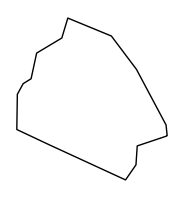

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[Line1=Line[Pin[[%]]]]
```

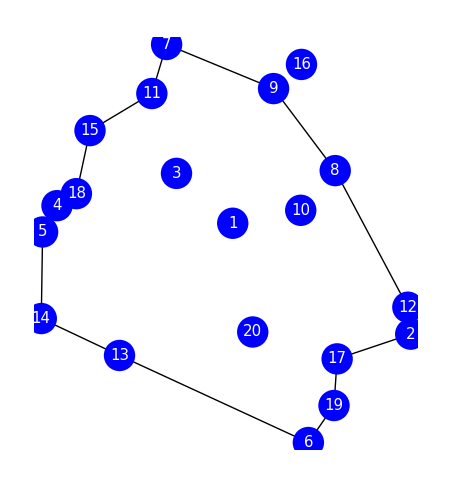

```mathematica
Graphics[{Line1,Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],

}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
OutVertex[PartLoop1]
```

{16}

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],{2,17,19,6,13,14,5,4,18,15,11,7,9,8,12,2}]
```

{10→16,20→10,16→3,10→3,1→3,20→16,3→20,1→16,10→1,20→1}

```mathematica
InsertVertex[PartLoop1,OutVertex[PartLoop1][[1]]]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,8→16,16→9}

```mathematica
PartLoop2={2->12,12->8,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2,8->16,16->9};
```

{2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,12,2}

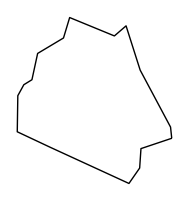

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutVertex[PartLoop2]
```

{}

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],{2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,12,2}]
```

{20→10,10→3,1→3,3→20,10→1,20→1}

```mathematica
PluralPartLoopByGreedyFromRank2[EdgeNumList[{20->10,10->3,1->3,3->20,10->1,20->1}]]
```

{20→10,10→3,3→20}

```mathematica
VertexSortFromLoopEdgeList[{20->10,10->3,3->20}]
Graphics[Line[Pin[[%]]]]
```

{3,20,10,3}

-Graphics-

```mathematica
RestVertex[Join[PartLoop2,{20->10,10->3,3->20}]]
```

{1}

```mathematica
InsertVertex[{20->10,10->3,3->20},RestVertex[Join[PartLoop2,{20->10,10->3,3->20}]][[1]]]
```

{20→10,10→3,1→3,20→1}

{1,20,10,3,1}

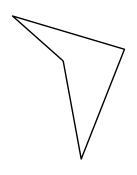

```mathematica
VertexSortFromLoopEdgeList[{20->10,10->3,1->3,20->1}]
Graphics[Line[Pin[[%]]]]
```

```mathematica
JoinPartLoop[PartLoop2,{20->10,10->3,1->3,20->1}]
```

{2→12,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,8→16,16→9,10→3,1→3,20→1,12→20,8→10}

{1,20,12,2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,10,3,1}

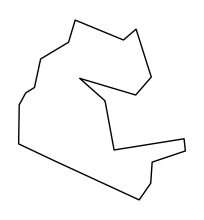

```mathematica
VertexSortFromLoopEdgeList[{2->12,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2,8->16,16->9,10->3,1->3,20->1,12->20,8->10}]
Graphics[Line[Pin[[%]]]]
```

```mathematica
PartLoop3=JoinPartLoop[PartLoop2,{20->10,10->3,3->20}]
```

{2→12,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,8→16,16→9,10→3,3→20,12→20,8→10}

{2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,10,3,20,12,2}

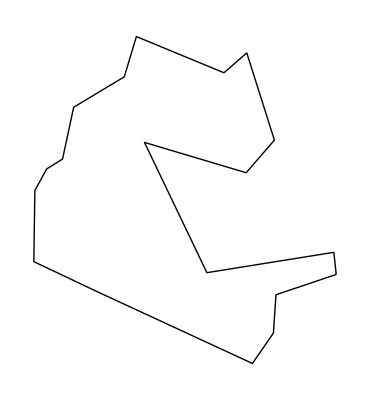

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
Graphics[Line[Pin[[%]]]]
```

```mathematica
Length[PartLoop3]
```

19

```mathematica
RestVertex[PartLoop3]
```

{1}

```mathematica
InsertVertexLoop[PartLoop3]
```

{2→12,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,8→16,16→9,10→3,12→20,8→10,3→1,1→20}

{1,20,12,2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,10,3,1}

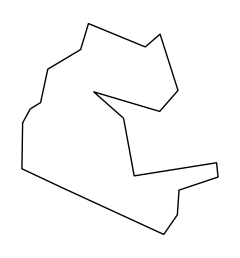

```mathematica
VertexSortFromLoopEdgeList[{2->12,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2,8->16,16->9,10->3,12->20,8->10,3->1,1->20}]
Graphics[Line[Pin[[%]]]]
```

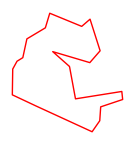

```mathematica
Graphics[{Red,Line[Pin[[{1,20,12,2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,10,3,1}]]]}]
```

```mathematica
ArcLength[Line[Pin[[{1,20,12,2,17,19,6,13,14,5,4,18,15,11,7,9,16,8,10,3,1}]]]]//N
```

37.8456

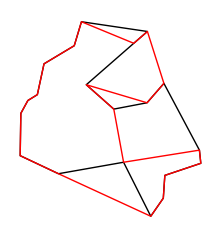

```mathematica
Show[-Graphics-,-Graphics-]
```

#### 8->16->7と通る場合

```mathematica
PartLoop8167={2->12,12->8,8->16,16->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2}
```

{2→12,12→8,8→16,16→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2}

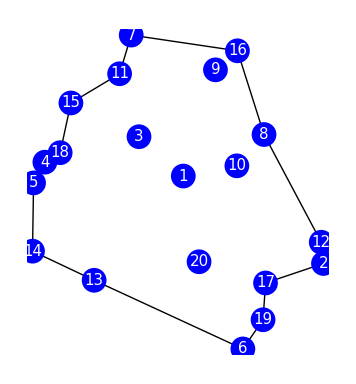

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop8167]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],

}]
```

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],VertexList[PartLoop8167]]
```

{10→9,9→3,20→10,10→3,1→3,20→9,3→20,1→9,10→1,20→1}

```mathematica
PartLoop81672={10->9,9->3,3->20,20->10};
```

```mathematica
PartLoop81672=PluralPartLoopByGreedyFromRank2[EdgeNumList[{10->9,9->3,20->10,10->3,1->3,20->9,3->20,1->9,10->1,20->1}]]
VertexSortFromLoopEdgeList[%]
Graphics[line=Line[Pin[[%]]]]
```

{10→9,9→3,3→20,20→10}

{3,9,10,20,3}

-Graphics-

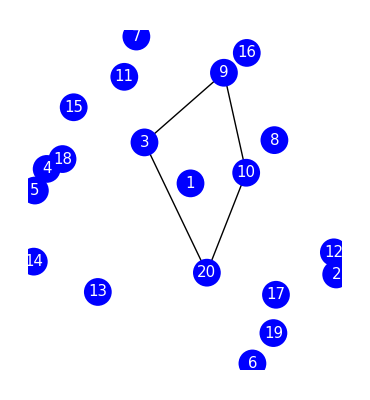

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop81672]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
PartLoop81673=InsertVertex[PartLoop81672,1]
```

{10→9,9→3,20→10,1→3,20→1}

```mathematica
VertexSortFromLoopEdgeList[PartLoop81673]
Graphics[line=Line[Pin[[%]]]]
```

{1,3,9,10,20,1}

-Graphics-

```mathematica
PartLoop81674=JoinPartLoop[PartLoop8167,PartLoop81673]
```

{2→12,12→8,16→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→6,6→19,19→17,17→2,9→3,20→10,1→3,20→1,8→10,16→9}

```mathematica
PartLoop81674={2->12,12->8,16->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->6,6->19,19->17,17->2,9->3,20->10,1->3,20->1,8->10,16->9};
```

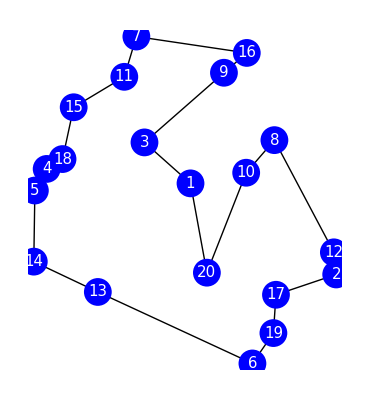

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop81674]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
ArcLength[line]//N
```

38.7209

#### 13->20->6と通る場合

```mathematica
PartLoop13206={2->12,12->8,8->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->20,20->6,6->19,19->17,17->2}
```

{2→12,12→8,8→9,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2}

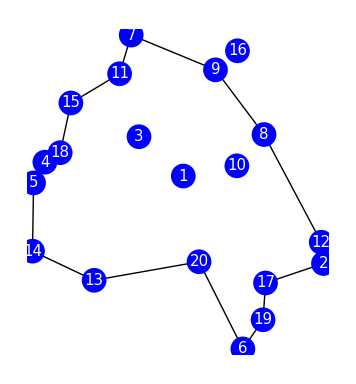

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop13206]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],

}]
```

```mathematica
OutVertex[PartLoop13206]
```

{16}

```mathematica
PartLoop132062=InsertVertex[PartLoop13206,OutVertex[PartLoop13206][[1]]]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2,8→16,16→9}

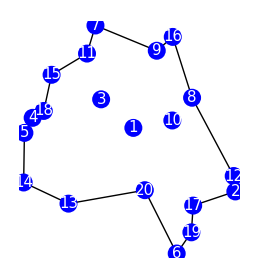

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132062]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],

}]
```

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],VertexList[PartLoop132062]]
```

{10→3,1→3,10→1}

```mathematica
PartLoop132063=InsertEdge[PartLoop132062,10->3]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2,16→9,10→3,8→10,16→3}

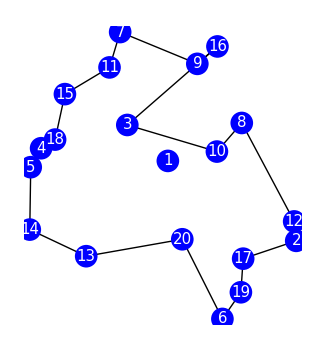

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132063]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
DelEleList[Range[Length[Pin]],VertexList[PartLoop132063]]
```

{1}

```mathematica
PartLoop132064=InsertVertex[PartLoop132063,1]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2,16→9,8→10,16→3,10→1,1→3}

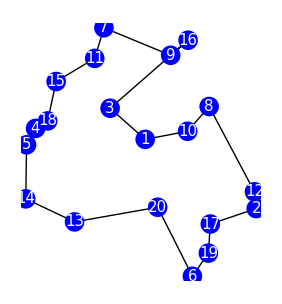

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132064]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
ArcLength[Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132064]]]]]//N
```

36.2506

#### 13->20->6と通る場合（内部から挿入する）

```mathematica
OutVertex[PartLoop13206]
```

{16}

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],Join[VertexList[PartLoop13206],OutVertex[PartLoop13206]]]
```

{10→3,1→3,10→1}

```mathematica
PartLoop132065=InsertEdge[PartLoop13206,10->3]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2,10→3,8→10,9→3}

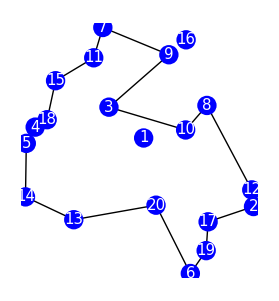

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132065]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop132065],OutVertex[PartLoop132065]]]
```

{1}

```mathematica
PartLoop132066=InsertVertex[PartLoop132065,1]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2,8→10,9→3,10→1,1→3}

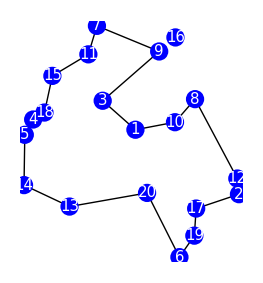

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132066]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop132066],OutVertex[PartLoop132066]]]
```

{}

```mathematica
OutVertex[PartLoop132066]
```

{16}

```mathematica
PartLoop132067=InsertVertex[PartLoop132066,16]
```

{2→12,12→8,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→6,6→19,19→17,17→2,8→10,9→3,10→1,1→3,16→9,16→7}

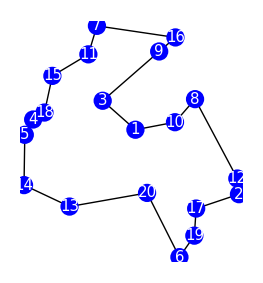

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop132067]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

#### 重み付け

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{49.8629,4.07094,34.9132,40.3098,62.853,40.8723,11.1199,18.903,3.42147,23.4094,42.5169,32.7971,52.8566,30.8472,32.2151,31.447,26.587,49.1235,9.63977,96.9825,170.065,177.121,22.1142,173.093,36.0746,94.76,28.477,148.979,0.766067,101.688,165.323,174.382,100.796,4.38454,157.058,8.63545,25.6529,13.4018,20.9849,108.745,15.5382,26.1498,15.1767,15.8626,5.12027,84.9459,41.363,45.3204,7.26833,28.8925,71.0896,7.93262,93.1767,33.9984,0.918227,143.961,43.6209,92.3907,71.8695,69.4187,21.4492,160.758,27.5382,10.7433,4.83164,95.7184,121.769,0.590782,139.934,65.2665,136.517,59.3056,107.653,87.0442,78.0288,34.4782,167.629,20.2214,5.71364,10.2846,114.706,123.046,2.04513,137.331,64.6393,199.127,88.8611,150.868,64.0656,178.437,30.0644,48.4586,103.966,175.797,172.004,6.25162,138.615,1.5902,13.703,50.5722,11.7116,52.2462,2.17215,152.058,119.34,110.766,11.3987,17.9699,153.368,33.2664,186.592,109.622,8.21784,2.35268,45.8835,24.4229,97.6621,129.358,73.0861,9.97662,39.0498,80.7194,66.4358,36.72,14.1075,12.6144,76.7669,115.433,127.783,38.5559,1.2167,90.9586,57.3326,124.701,70.2395,39.6532,19.73,63.4206,93.9637,59.9224,20.6278,23.7934,58.7645,44.8027,16.6437,131.92,82.727,74.43,3.73381,22.9596,125.794,14.4722,155.754,79.3098,102.512,162.255,158.362,83.692,5.98066,146.791,13.0333,25.1382,5.49801,60.9352,142.314,54.2892,29.5958,55.4604,17.5089,43.0126,159.311,106.805,16.2019,112.832,51.3563,56.3219,134.685,3.04149,163.624,78.6705,105.553,80.045,141.314,87.8048,116.276,1.76236,6.46299,132.727,58.0486,9.29091}

```mathematica
PDWeight=PD*Table[i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{44.926,2.30096,30.7568,35.8309,57.3875,36.3808,8.40775,15.5867,1.7922,19.808,37.9452,28.6974,47.8226,26.8411,28.1372,27.4154,22.8423,44.2112,7.03442,90.2941,161.208,168.13,18.604,164.171,31.8305,88.1334,24.576,140.656,0.127678,94.8168,156.622,165.439,93.9394,2.55765,148.522,6.16818,21.9351,10.4884,17.5448,101.684,12.4915,22.4141,12.1413,12.8121,3.15093,78.6536,36.867,40.6482,4.99697,24.9882,65.31,5.5288,86.5685,29.8522,0.211899,135.827,39.0292,85.7914,66.0736,63.6816,17.9897,152.162,23.7134,8.05746,2.89898,89.0713,114.253,0.0537075,131.892,59.7819,128.533,54.0104,100.617,80.6438,71.9328,30.3242,158.853,16.794,3.67305,7.6475,107.446,115.497,0.842112,129.346,59.1614,189.17,82.4219,142.486,58.5899,169.425,26.1086,43.5637,97.0346,166.828,163.092,4.16775,130.602,0.530065,10.7874,45.6141,8.98796,47.2225,0.965402,143.657,111.927,103.665,8.68471,14.761,144.941,29.1595,177.216,102.55,5.80083,1.11443,41.2015,20.7777,90.9729,121.612,67.2393,7.35119,34.6123,74.6043,60.8995,32.4503,11.1684,9.74753,70.7223,108.173,120.086,34.1242,0.347629,84.4148,52.0727,117.097,64.4821,35.1978,16.3283,57.9533,87.3465,54.6195,17.1898,20.1884,53.4704,40.1358,13.5615,124.068,76.5069,68.5229,2.03662,19.3721,118.17,11.5187,147.243,73.2091,95.632,153.624,149.802,77.4463,3.91836,138.545,10.137,21.4414,3.46171,55.59,134.228,49.1676,25.6497,50.2772,14.3254,38.4368,150.746,99.7784,13.145,105.645,46.3702,51.1069,126.762,1.52074,154.967,72.572,98.5632,73.9347,133.239,81.3957,109.009,0.660884,4.37816,124.873,52.7715,6.7101}

```mathematica
PDWeightCurrRank=Ordering[Abs[PDWeight/Curr]]
```

{68,29,55,98,131,186,83,103,178,149,34,163,65,79,114,159,36,96,113,120,64,107,101,80,187,161,126,108,152,52,173,78,23,169,190,125,116,150,49,61,2,137,63,91,43,38,141,45,167,110,25,145,92,142,76,99,130,37,27,170,57,162,44,121,168,39,9,166,100,42,175,115,176,50,72,41,124,158,136,127,164,93,144,133,102,123,33,85,148,26,174,59,48,47,70,182,189,172,30,119,87,181,106,89,66,155,132,10,8,71,74,147,140,11,84,56,81,183,138,97,104,82,54,134,122,184,69,6,15,105,31,135,146,14,180,188,24,46,67,1,156,12,16,19,58,95,143,28,185,129,88,117,94,20,171,109,22,17,40,13,73,60,139,157,179,77,151,4,21,7,111,128,18,154,32,35,53,177,62,90,5,165,51,118,153,3,75,112,86,160}

```mathematica
PDWeightCurrRank={29,68,55,98,186,83,178,131,103,149,163,79,34,65,159,114,36,96,113,120,64,101,107,80,187,161,126,108,152,173,78,23,52,169,125,116,190,150,61,63,49,91,137,141,43,38,167,25,110,92,2,145,76,142,130,37,170,57,99,27,45,121,162,168,44,166,100,39,175,176,115,42,50,72,158,124,127,136,164,41,93,144,133,123,102,9,33,85,148,26,174,59,48,182,70,47,189,172,30,119,87,106,181,89,66,155,71,132,74,147,10,8,140,56,84,11,81,183,97,104,138,82,134,54,69,122,184,31,105,146,135,6,15,188,180,24,14,46,67,156,1,95,12,58,16,28,185,143,129,88,117,19,94,20,171,109,22,40,73,60,13,139,17,157,179,77,151,21,4,111,128,7,154,18,32,35,53,177,62,90,5,165,51,118,153,75,3,112,86,160};
```

```mathematica
PartLoop1=PluralPartLoopByGreedyFromRank2[PDWeightCurrRank]
```

{18→4,4→5,5→14,14→13,13→20,20→17,17→2,2→12,12→8,8→9,9→7,7→11,11→15,15→18}

```mathematica
PartLoop1={2->12,12->8,8->9,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->20,20->17,17->2};
```

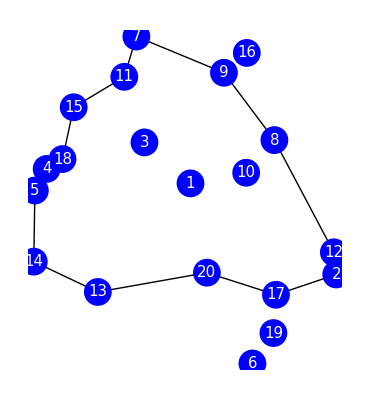

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop1]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

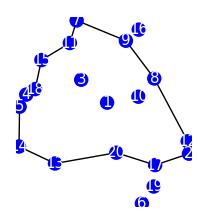

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop1]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
OutVertex[PartLoop1]
```

{6,16,19}

#### 内部の点から挿入する

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],Join[{2,17,20,13,14,5,4,18,15,11,7,9,8,12,2},{6,16,19}]]
```

{10→3,1→3,10→1}

```mathematica
PartLoop2=InsertEdge[PartLoop1,10->3]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→17,17→2,10→3,8→10,9→3}

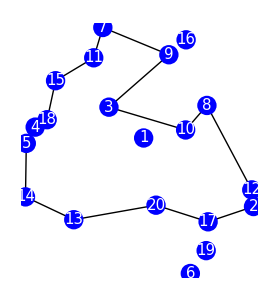

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop2]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
PartLoop3=InsertVertex[PartLoop2,1]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,20→17,17→2,8→10,9→3,10→1,1→3}

```mathematica
PartLoop3={2->12,12->8,9->7,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->20,20->17,17->2,8->10,9->3,10->1,1->3};
```

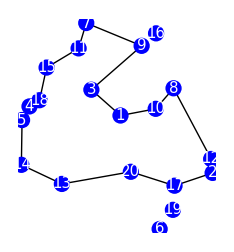

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop3]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

#### PartLoopを含めた頂点と外側の点とで構成する枝はPartLoopとクロスする可能性がある(?)

```mathematica
MostOutEdge[PartLoop3,PDCurrCostSort]
```

186

```mathematica
OutEdgeList
```

{186,36,131,108,120,161,96,23,150,92,91,168,141,93,158,176,190,33,174,123,71,50,144,182,181,99,87,66,56,84,97,89,81,69,134,188,184,88,94,171,15,40,179,111,90,53,18,165,153,5,86}

```mathematica
EdgeRules[Gout][[186]]
```

19→17

```mathematica
MostOutEdge[PartLoop3,PDWeightCurrRank]
```

186

```mathematica
OutEdgeList
```

{186,131,36,96,120,161,108,23,190,150,91,141,92,99,168,176,50,158,93,144,123,33,174,182,87,181,89,66,71,56,84,81,97,134,69,184,15,188,88,94,171,40,179,111,18,53,90,5,165,153,86}

```mathematica
EdgeRules[Gout][[131]]
```

16→9

```mathematica
EdgeRules[Gout][[36]]
```

19→2

```mathematica
OutEdgeRank[PartLoop3,PDWeightCurrRank]
```

{98,186,131,36,96,120,161,108,23,190,150,91,141,92,99,168,176,50,158,93,144,123,33,174,182,87,181,89,66,71,56,84,81,183,97,134,69,184,15,188,95,88,94,171,40,179,111,18,53,90,5,165,153,86}

#### 最初にできたPartLoopの中で最もランクが低い枝よりもランクが高い、PartLoopの点を含まない枝を挿入する（挿入する枝をPartLoopとクロスしないと予想する）

```mathematica
Subsets[OutVertex[PartLoop3],{2}]
```

{{6,16},{6,19},{16,19}}

```mathematica
EdgeNumListVertex[Subsets[OutVertex[PartLoop3],{2}]]
```

{95,98,183}

```mathematica
SortSameAs[PDWeightCurrRank,EdgeNumListVertex[Subsets[OutVertex[PartLoop3],{2}]]]
```

{98,183,95}

```mathematica
SortSameAs[PDWeightCurrRank,Join[{98,183,95},EdgeNumList[PartLoop1]]]
```

{29,68,55,98,178,103,149,163,79,34,113,101,187,169,116,183,95}

```mathematica
SortSameAs[PDWeightCurrRank,EdgeNumList[PartLoop1]]
```

{29,68,55,178,103,149,163,79,34,113,101,187,169,116}

```mathematica
SortSameAs[PDWeightCurrRank,EdgeNumList[PartLoop1]][[-1]]
```

116

```mathematica
FirstPosition[PDWeightCurrRank,116]
```

{36}

```mathematica
Table[FirstPosition[PDWeightCurrRank,i],{i,{95,98,183}}](* 98は116よりランクが高い *)
```

{{142},{4},{118}}

```mathematica
PartLoop4=InsertEdge[PartLoop3,EdgeRules[Gout][[98]]]
```

{2→12,12→8,9→7,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,17→2,8→10,9→3,10→1,1→3,6→19,20→6,17→19}

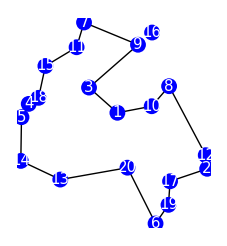

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop4]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
OutVertex[PartLoop4]
```

{16}

```mathematica
InsertVertex[PartLoop4,OutVertex[PartLoop4][[1]]]
```

{2→12,12→8,7→11,11→15,15→18,18→4,4→5,5→14,14→13,13→20,17→2,8→10,9→3,10→1,1→3,6→19,20→6,17→19,16→9,16→7}

```mathematica
PartLoop5={2->12,12->8,7->11,11->15,15->18,18->4,4->5,5->14,14->13,13->20,17->2,8->10,9->3,10->1,1->3,6->19,20->6,17->19,16->9,16->7};
```

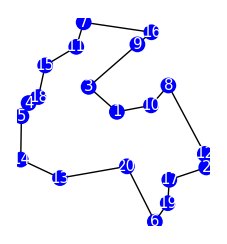

```mathematica
Graphics[{Line[Pin[[VertexSortFromLoopEdgeList[PartLoop5]]]],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
Length[VertexList[PartLoop5]]
```

20

```mathematica
MeshRegion[{{0,0},{1,0},{2,1/2},{2,-1/2}},{Line[{1,2}],Line[{2,3}],Line[{3,4}],Line[{4,2}]}];
HighlightMesh[%,Labeled[0,"Index"]]
```

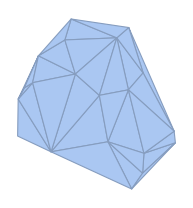

```mathematica
DelaunayMesh[Pin]
```

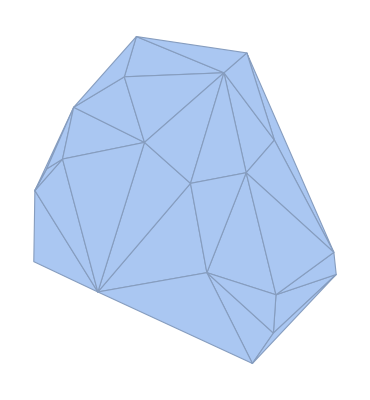
```mathematica
HighlightMesh[-Graphics-,Labeled[0,"Index"]]
```

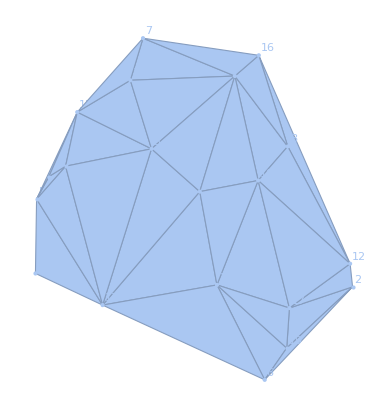

```mathematica
MeshCells[-Graphics-,1]
```

{Line[{5,14}],Line[{14,13}],Line[{13,5}],Line[{13,18}],Line[{18,5}],Line[{18,4}],Line[{4,5}],Line[{1,13}],Line[{13,20}],Line[{20,1}],Line[{3,13}],Line[{1,3}],Line[{4,15}],Line[{15,5}],Line[{18,15}],Line[{18,3}],Line[{3,15}],Line[{7,11}],Line[{11,9}],Line[{9,7}],Line[{3,11}],Line[{11,15}],Line[{3,9}],Line[{7,15}],Line[{1,9}],Line[{20,6}],Line[{6,19}],Line[{19,20}],Line[{13,6}],Line[{19,2}],Line[{2,17}],Line[{17,19}],Line[{6,2}],Line[{20,17}],Line[{17,10}],Line[{10,20}],Line[{12,17}],Line[{2,12}],Line[{9,10}],Line[{10,8}],Line[{8,9}],Line[{1,10}],Line[{16,8}],Line[{8,12}],Line[{12,16}],Line[{16,9}],Line[{10,12}],Line[{16,7}]}

```mathematica
EdgeNumListLine[MeshCells[-Graphics-,1]]
```

{79,163,78,167,83,68,55,12,169,19,47,2,65,80,178,52,49,103,126,101,45,149,43,107,8,99,98,190,92,36,34,186,23,187,142,145,159,29,125,114,113,9,120,116,158,131,137,108}

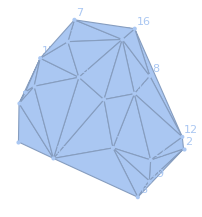
```mathematica
EdgeRulesMesh[-Graphics-]
```

{5→14,14→13,5→13,18→13,18→5,18→4,4→5,13→1,13→20,20→1,3→13,1→3,15→4,15→5,15→18,3→18,3→15,7→11,9→11,9→7,11→3,11→15,9→3,7→15,1→9,20→6,6→19,20→19,13→6,19→2,17→2,19→17,6→2,20→17,17→10,20→10,17→12,2→12,10→9,10→8,8→9,10→1,8→16,12→8,12→16,16→9,12→10,16→7}